```mathematica
func2[x_,a_,P_]:=P (1.00-a^x) (*P is power aim, a determines rate*)
```

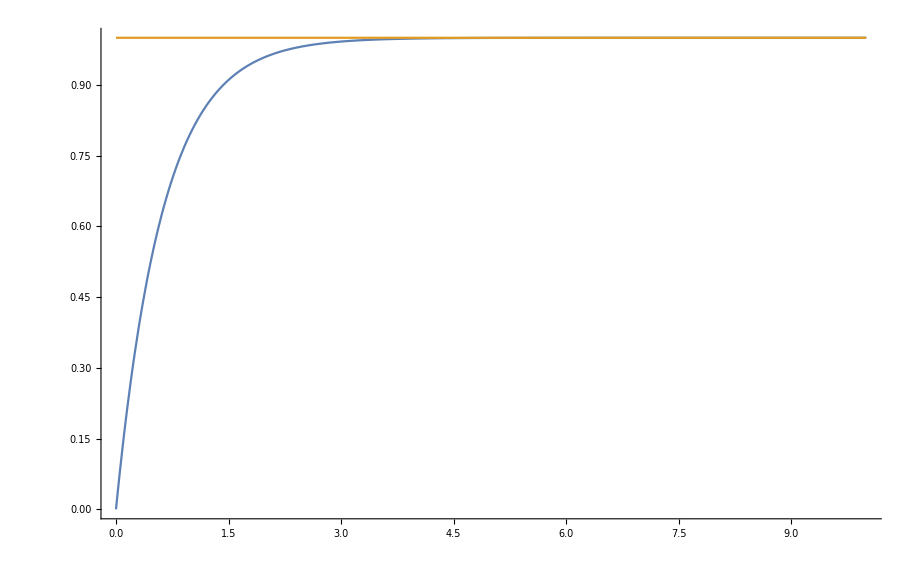

```mathematica
Plot[{func2[x,0.2,1], 1}, {x,0,10}, PlotRange->All]
```

```mathematica
pulsestoreachpower=600; (*should be total pulses rather than time*)
```

```mathematica
funcmax[percent_,a_]:=(Log10[1-percent/100])/(Log10[a])(*x value that gives a certain percentage of power required*)
```

```mathematica
steppulses=5;(*pulses at each power step*)
```

```mathematica
nsteps=pulsestoreachpower/steppulses;
```

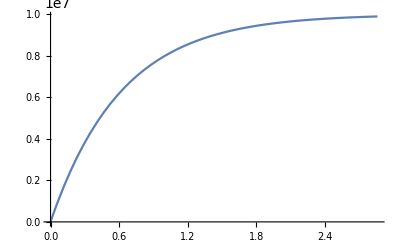

```mathematica
Plot[func2[x,0.2,1*^7], {x,0,funcmax[99,0.2]}] (*plot of function up to 99 percent of 10 MW*)
```

```mathematica
xsteps=Drop[Range[0,funcmax[99,0.2], funcmax[99,0.2]/(nsteps)],1];
```

```mathematica
ysteps[a_,P_]:=func2[#,a,P]&/@xsteps
```

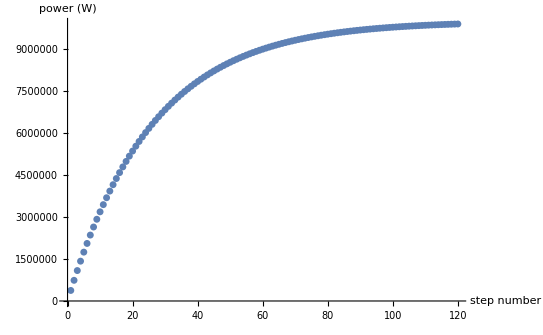

```mathematica
ListPlot[ysteps[0.2,1*^7], AxesLabel->{"step number","power (W)" }] (*Plot of function against step number, with 5 pulses at each step*)
```

```mathematica
repeat[list_,n_]:=Sequence@@ConstantArray[#,n]&/@list
```

```mathematica
repeat[func2[#,0.1,1*^7]&/@xsteps,steppulses];
```

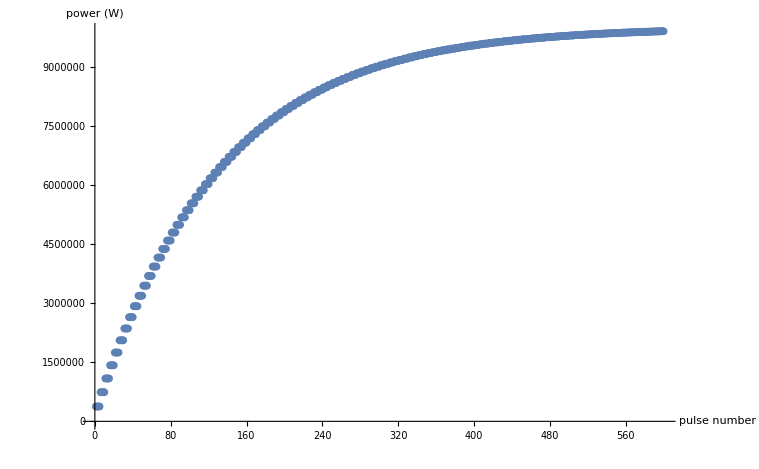

```mathematica
ListPlot[repeat[ysteps[0.2,1*^7],steppulses],AxesLabel->{"pulse number","power (W)" }](*Same plot as above but against pulse number*)
```

We need to define a max value for y steps and a min value for xsteps 
10 kW (??) and x pulses 
at 100Hz, probably 100Hx (??)

```mathematica
repeat[ysteps[0.2,0.3 10^6],steppulses]
```

{11294.8,11294.8,11294.8,11294.8,11294.8,22164.4,22164.4,22164.4,22164.4,22164.4,32624.7,32624.7,32624.7,32624.7,32624.7,42691.2,42691.2,42691.2,42691.2,42691.2,52378.7,52378.7,52378.7,52378.7,52378.7,61701.5,61701.5,61701.5,61701.5,61701.5,70673.3,70673.3,70673.3,70673.3,70673.3,79307.3,79307.3,79307.3,79307.3,79307.3,87616.3,87616.3,87616.3,87616.3,87616.3,95612.4,95612.4,95612.4,95612.4,95612.4,103307.,103307.,103307.,103307.,103307.,110713.,110713.,110713.,110713.,110713.,117839.,117839.,117839.,117839.,117839.,124698.,124698.,124698.,124698.,124698.,131298.,131298.,131298.,131298.,131298.,137649.,137649.,137649.,137649.,137649.,143762.,143762.,143762.,143762.,143762.,149644.,149644.,149644.,149644.,149644.,155305.,155305.,155305.,155305.,155305.,160752.,160752.,160752.,160752.,160752.,165995.,165995.,165995.,165995.,165995.,171040.,171040.,171040.,171040.,171040.,175895.,175895.,175895.,175895.,175895.,180568.,180568.,180568.,180568.,180568.,185064.,185064.,185064.,185064.,185064.,189392.,189392.,189392.,189392.,189392.,193556.,193556.,193556.,193556.,193556.,197564.,197564.,197564.,197564.,197564.,201420.,201420.,201420.,201420.,201420.,205132.,205132.,205132.,205132.,205132.,208703.,208703.,208703.,208703.,208703.,212141.,212141.,212141.,212141.,212141.,215449.,215449.,215449.,215449.,215449.,218632.,218632.,218632.,218632.,218632.,221695.,221695.,221695.,221695.,221695.,224643.,224643.,224643.,224643.,224643.,227481.,227481.,227481.,227481.,227481.,230211.,230211.,230211.,230211.,230211.,232838.,232838.,232838.,232838.,232838.,235367.,235367.,235367.,235367.,235367.,237800.,237800.,237800.,237800.,237800.,240142.,240142.,240142.,240142.,240142.,242396.,242396.,242396.,242396.,242396.,244565.,244565.,244565.,244565.,244565.,246652.,246652.,246652.,246652.,246652.,248660.,248660.,248660.,248660.,248660.,250593.,250593.,250593.,250593.,250593.,252453.,252453.,252453.,252453.,252453.,254243.,254243.,254243.,254243.,254243.,255966.,255966.,255966.,255966.,255966.,257624.,257624.,257624.,257624.,257624.,259219.,259219.,259219.,259219.,259219.,260755.,260755.,260755.,260755.,260755.,262232.,262232.,262232.,262232.,262232.,263654.,263654.,263654.,263654.,263654.,265023.,265023.,265023.,265023.,265023.,266339.,266339.,266339.,266339.,266339.,267607.,267607.,267607.,267607.,267607.,268826.,268826.,268826.,268826.,268826.,270000.,270000.,270000.,270000.,270000.,271129.,271129.,271129.,271129.,271129.,272216.,272216.,272216.,272216.,272216.,273262.,273262.,273262.,273262.,273262.,274269.,274269.,274269.,274269.,274269.,275238.,275238.,275238.,275238.,275238.,276170.,276170.,276170.,276170.,276170.,277067.,277067.,277067.,277067.,277067.,277931.,277931.,277931.,277931.,277931.,278762.,278762.,278762.,278762.,278762.,279561.,279561.,279561.,279561.,279561.,280331.,280331.,280331.,280331.,280331.,281071.,281071.,281071.,281071.,281071.,281784.,281784.,281784.,281784.,281784.,282470.,282470.,282470.,282470.,282470.,283130.,283130.,283130.,283130.,283130.,283765.,283765.,283765.,283765.,283765.,284376.,284376.,284376.,284376.,284376.,284964.,284964.,284964.,284964.,284964.,285530.,285530.,285530.,285530.,285530.,286075.,286075.,286075.,286075.,286075.,286599.,286599.,286599.,286599.,286599.,287104.,287104.,287104.,287104.,287104.,287590.,287590.,287590.,287590.,287590.,288057.,288057.,288057.,288057.,288057.,288506.,288506.,288506.,288506.,288506.,288939.,288939.,288939.,288939.,288939.,289356.,289356.,289356.,289356.,289356.,289756.,289756.,289756.,289756.,289756.,290142.,290142.,290142.,290142.,290142.,290513.,290513.,290513.,290513.,290513.,290870.,290870.,290870.,290870.,290870.,291214.,291214.,291214.,291214.,291214.,291545.,291545.,291545.,291545.,291545.,291863.,291863.,291863.,291863.,291863.,292170.,292170.,292170.,292170.,292170.,292464.,292464.,292464.,292464.,292464.,292748.,292748.,292748.,292748.,292748.,293021.,293021.,293021.,293021.,293021.,293284.,293284.,293284.,293284.,293284.,293537.,293537.,293537.,293537.,293537.,293780.,293780.,293780.,293780.,293780.,294014.,294014.,294014.,294014.,294014.,294240.,294240.,294240.,294240.,294240.,294456.,294456.,294456.,294456.,294456.,294665.,294665.,294665.,294665.,294665.,294866.,294866.,294866.,294866.,294866.,295059.,295059.,295059.,295059.,295059.,295245.,295245.,295245.,295245.,295245.,295424.,295424.,295424.,295424.,295424.,295597.,295597.,295597.,295597.,295597.,295762.,295762.,295762.,295762.,295762.,295922.,295922.,295922.,295922.,295922.,296075.,296075.,296075.,296075.,296075.,296223.,296223.,296223.,296223.,296223.,296365.,296365.,296365.,296365.,296365.,296502.,296502.,296502.,296502.,296502.,296634.,296634.,296634.,296634.,296634.,296761.,296761.,296761.,296761.,296761.,296883.,296883.,296883.,296883.,296883.,297000.,297000.,297000.,297000.,297000.}

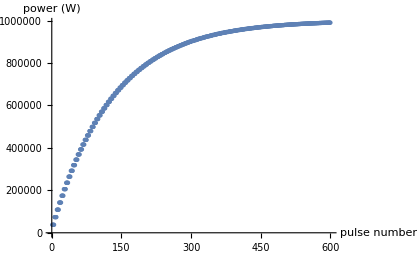

```mathematica
ListPlot[repeat[ysteps[0.2,0.1*^7],steppulses],AxesLabel->{"pulse number","power (W)" }]
```

```mathematica
ysteps[0.1,0.3*^7]
```

{160273.,311983.,455588.,591521.,720192.,841989.,957279.,1.06641×10^6,1.16971×10^6,1.26749×10^6,1.36005×10^6,1.44766×10^6,1.5306×10^6,1.6091×10^6,1.68341×10^6,1.75374×10^6,1.82032×10^6,1.88335×10^6,1.943×10^6,1.99947×10^6,2.05292×10^6,2.10352×10^6,2.15142×10^6,2.19675×10^6,2.23966×10^6,2.28028×10^6,2.31873×10^6,2.35513×10^6,2.38958×10^6,2.42219×10^6,2.45306×10^6,2.48228×10^6,2.50994×10^6,2.53612×10^6,2.5609×10^6,2.58436×10^6,2.60657×10^6,2.62759×10^6,2.64748×10^6,2.66631×10^6,2.68414×10^6,2.70102×10^6,2.71699×10^6,2.73211×10^6,2.74642×10^6,2.75997×10^6,2.77279×10^6,2.78493×10^6,2.79642×10^6,2.8073×10^6,2.81759×10^6,2.82734×10^6,2.83656×10^6,2.84529×10^6,2.85356×10^6,2.86138×10^6,2.86879×10^6,2.8758×10^6,2.88243×10^6,2.88871×10^6,2.89466×10^6,2.90029×10^6,2.90561×10^6,2.91066×10^6,2.91543×10^6,2.91995×10^6,2.92422×10^6,2.92827×10^6,2.9321×10^6,2.93573×10^6,2.93916×10^6,2.94241×10^6,2.94549×10^6,2.9484×10^6,2.95116×10^6,2.95377×10^6,2.95624×10^6,2.95858×10^6,2.96079×10^6,2.96288×10^6,2.96487×10^6,2.96674×10^6,2.96852×10^6,2.9702×10^6,2.97179×10^6,2.9733×10^6,2.97473×10^6,2.97608×10^6,2.97736×10^6,2.97857×10^6,2.97971×10^6,2.98079×10^6,2.98182×10^6,2.98279×10^6,2.98371×10^6,2.98458×10^6,2.98541×10^6,2.98619×10^6,2.98692×10^6,2.98762×10^6,2.98828×10^6,2.98891×10^6,2.9895×10^6,2.99006×10^6,2.99059×10^6,2.9911×10^6,2.99157×10^6,2.99202×10^6,2.99245×10^6,2.99285×10^6,2.99323×10^6,2.99359×10^6,2.99394×10^6,2.99426×10^6,2.99457×10^6,2.99486×10^6,2.99513×10^6,2.99539×10^6,2.99564×10^6,2.99587×10^6}

```mathematica
func2[x_,a_,P_]:=P (1.00-a^x) (*P is power aim, a determines rate*)
```

```mathematica
rampCurve[x_,a_,P_]:=P (1.00-a^x) (*P is power aim, a determines rate*)
```

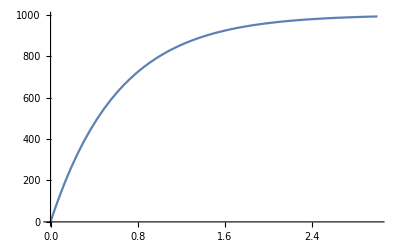

```mathematica
Plot[P (1.00-a^x)/.{P->1000,a->0.2},{x,0,3}]
```

### DJS

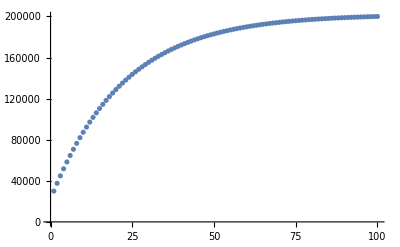

```mathematica
(* Curve Formula  Pfinish * (1.00-ramprate^x) *)
(* define a start and end power in watts *)
Pstart=30000;
requestPfinish=200000;
curvePfinish=1.01 200000;
(* ramp rate is related to the curve gradient change with x *)
ramprate=0.2;
(* find the values for x for the start and finish powers *)
x0=Log[ramprate,(1-Pstart/curvePfinish)];
x1=Log[ramprate,(1-requestPfinish/curvePfinish)];
(* define number of steps to ramp over *)
numsteps = 100;
curve=rampCurve[#,ramprate,curvePfinish]&/@Range[x0,x1,(x1-x0)/(numsteps-1)];
ListPlot[curve]
```

```mathematica
binx={550.0,650.0,750.0,850.0,950.0,1050.0,1150.0,1250.0,1350.0,1450.0,1550.0,1650.0,1750.0,1850.0,1950.0,2050.0,2150.0,2250.0,2350.0,2450.0,2550.0,2650.0,2750.0,2850.0,2950.0,3050.0,3150.0,3250.0,3350.0,3450.0,3550.0,3650.0,3750.0,3850.0,3950.0,4050.0,4150.0,4250.0,4350.0,4450.0,4550.0,4650.0,4750.0,4850.0,4950.0,5050.0,5150.0,5250.0,5350.0,5450.0,5550.0,5650.0,5750.0,5850.0,5950.0,6050.0,6150.0,6250.0,6350.0,6450.0,6550.0,6650.0,6750.0,6850.0,6950.0,7050.0,7150.0,7250.0,7350.0,7450.0,7550.0,7650.0,7750.0,7850.0,7950.0,8050.0,8150.0,8250.0,8350.0,8450.0,8550.0,8650.0,8750.0,8850.0,8950.0,9050.0,9150.0,9250.0,9350.0,9450.0,9550.0,9650.0,9750.0,9850.0,9950.0,10050.0,10150.0,10250.0,10350.0,10450.0,10550.0,10650.0,10750.0,10850.0,10950.0,11050.0,11150.0,11250.0,11350.0,11450.0,11550.0,11650.0,11750.0,11850.0,11950.0,12050.0,12150.0,12250.0,12350.0,12450.0,12550.0,12650.0,12750.0,12850.0,12950.0,13050.0,13150.0,13250.0,13350.0,13450.0,13550.0,13650.0,13750.0,13850.0,13950.0,14050.0,14150.0,14250.0,14350.0,14450.0,14550.0,14650.0,14750.0,14850.0,14950.0,15050.0,15150.0,15250.0,15350.0,15450.0,15550.0,15650.0,15750.0,15850.0,15950.0,16050.0,16150.0,16250.0,16350.0,16450.0,16550.0,16650.0,16750.0,16850.0,16950.0,17050.0,17150.0,17250.0,17350.0,17450.0,17550.0,17650.0,17750.0,17850.0,17950.0,18050.0,18150.0,18250.0,18350.0,18450.0,18550.0,18650.0,18750.0,18850.0,18950.0,19050.0,19150.0,19250.0,19350.0,19450.0,19550.0,19650.0,19750.0,19850.0,19950.0,20050.0,20150.0,20250.0,20350.0,20450.0,20550.0,20650.0,20750.0,20850.0,20950.0,21050.0,21150.0,21250.0,21350.0,21450.0,21550.0,21650.0,21750.0,21850.0,21950.0,22050.0,22150.0,22250.0,22350.0,22450.0,22550.0,22650.0,22750.0,22850.0,22950.0,23050.0,23150.0,23250.0,23350.0,23450.0,23550.0,23650.0,23750.0,23850.0,23950.0,24050.0,24150.0,24250.0,24350.0,24450.0,24550.0,24650.0,24750.0,24850.0,24950.0,25050.0,25150.0,25250.0,25350.0,25450.0,25550.0,25650.0,25750.0,25850.0,25950.0,26050.0,26150.0,26250.0,26350.0,26450.0,26550.0,26650.0,26750.0,26850.0,26950.0,27050.0,27150.0,27250.0,27350.0,27450.0,27550.0,27650.0,27750.0,27850.0,27950.0,28050.0,28150.0,28250.0,28350.0,28450.0,28550.0,28650.0,28750.0,28850.0,28950.0,29050.0,29150.0,29250.0,29350.0,29450.0,29550.0,29650.0,29750.0,29850.0,29950.0,30050.0,30150.0,30250.0,30350.0,30450.0,30550.0,30650.0,30750.0,30850.0,30950.0,31050.0,31150.0,31250.0,31350.0,31450.0,31550.0,31650.0,31750.0,31850.0,31950.0,32050.0,32150.0,32250.0,32350.0,32450.0,32550.0,32650.0,32750.0,32850.0,32950.0,33050.0,33150.0,33250.0,33350.0,33450.0,33550.0,33650.0,33750.0,33850.0,33950.0,34050.0,34150.0,34250.0,34350.0,34450.0,34550.0,34650.0,34750.0,34850.0,34950.0,35050.0,35150.0,35250.0,35350.0,35450.0,35550.0,35650.0,35750.0,35850.0,35950.0,36050.0,36150.0,36250.0,36350.0,36450.0,36550.0,36650.0,36750.0,36850.0,36950.0,37050.0,37150.0,37250.0,37350.0,37450.0,37550.0,37650.0,37750.0,37850.0,37950.0,38050.0,38150.0,38250.0,38350.0,38450.0,38550.0,38650.0,38750.0,38850.0,38950.0,39050.0,39150.0,39250.0,39350.0,39450.0,39550.0,39650.0,39750.0,39850.0,39950.0,40050.0,40150.0,40250.0,40350.0,40450.0,40550.0,40650.0,40750.0,40850.0,40950.0,41050.0,41150.0,41250.0,41350.0,41450.0,41550.0,41650.0,41750.0,41850.0,41950.0,42050.0,42150.0,42250.0,42350.0,42450.0,42550.0,42650.0,42750.0,42850.0,42950.0,43050.0,43150.0,43250.0,43350.0,43450.0,43550.0,43650.0,43750.0,43850.0,43950.0,44050.0,44150.0,44250.0,44350.0,44450.0,44550.0,44650.0,44750.0,44850.0,44950.0,45050.0,45150.0,45250.0,45350.0,45450.0,45550.0,45650.0,45750.0,45850.0,45950.0,46050.0,46150.0,46250.0,46350.0,46450.0,46550.0,46650.0,46750.0,46850.0,46950.0,47050.0,47150.0,47250.0,47350.0,47450.0,47550.0,47650.0,47750.0,47850.0,47950.0,48050.0,48150.0,48250.0,48350.0,48450.0,48550.0,48650.0,48750.0,48850.0,48950.0,49050.0,49150.0,49250.0,49350.0,49450.0,49550.0,49650.0,49750.0,49850.0,49950.0,50050.0,50150.0,50250.0,50350.0,50450.0,50550.0,50650.0,50750.0,50850.0,50950.0,51050.0,51150.0,51250.0,51350.0,51450.0,51550.0,51650.0,51750.0,51850.0,51950.0,52050.0,52150.0,52250.0,52350.0,52450.0,52550.0,52650.0,52750.0,52850.0,52950.0,53050.0,53150.0,53250.0,53350.0,53450.0,53550.0,53650.0,53750.0,53850.0,53950.0,54050.0,54150.0,54250.0,54350.0,54450.0,54550.0,54650.0,54750.0,54850.0,54950.0,55050.0,55150.0,55250.0,55350.0,55450.0,55550.0,55650.0,55750.0,55850.0,55950.0,56050.0,56150.0,56250.0,56350.0,56450.0,56550.0,56650.0,56750.0,56850.0,56950.0,57050.0,57150.0,57250.0,57350.0,57450.0,57550.0,57650.0,57750.0,57850.0,57950.0,58050.0,58150.0,58250.0,58350.0,58450.0,58550.0,58650.0,58750.0,58850.0,58950.0,59050.0,59150.0,59250.0,59350.0,59450.0,59550.0,59650.0,59750.0,59850.0};
biny={1134.99538311,1573.99183825,2190.69134998 2461.25082853,3235.1122837,4015.98002987,4695.7090784,6193.15183168,6612.67492499,7634.55866495,8503.9821383,9778.50105477,10713.6275949,12231.83592516,14063.16056061,15084.97756335,16759.12076478,18296.25416894,19853.37870186,21664.30155878,23307.14284646,25373.523336,27710.00661915,30072.86625581,31714.90006167,33490.82774898,35407.49384895,37796.39656541,40707.2989268,43742.46201703,46020.66678571,49015.88378408,51396.06997227,53873.07127439,56524.39508313,59766.38534482,63800.1040219,66592.52873997,69219.29278304,72421.69034538,75861.61135726,79790.16698567,82874.20337484,85616.04194107,89384.4425943,93653.89972667,98285.8387803,101155.17047828,105294.69006123,109326.01039668,113177.0203025,117577.30067932,122339.74528867,127849.02446214,131602.38019581,135248.49040239,139841.58891392,144590.868719,149755.7885763,154640.58696582,159421.76410499,164641.77524437,168912.0899752,175879.78287949,180462.66686123,184094.06076915,188006.75263638,195425.35903746,200634.14189979,205178.19392018,210207.16826726,217580.1187646,221206.35690099,227760.93551504,233880.67690924,239469.73632993,245407.43902251,251826.21972826,257773.29656596,264132.09024927,269801.67694932,275825.35174115,281718.1081175,288817.61502904,295457.24989728,300921.63692126,307493.56569667,314091.287691,320389.21295983,327058.96066647,333951.3039359,341282.6488014,347397.25276041,353794.65615639,361468.57336227,369044.72687247,377244.74453604,383821.89780175,391115.30712032,395053.92060417};
```

```mathematica
ifunc=Interpolation[Transpose[{biny,binx⟦1;;Length@biny⟧}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Prime[Range@29]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109}

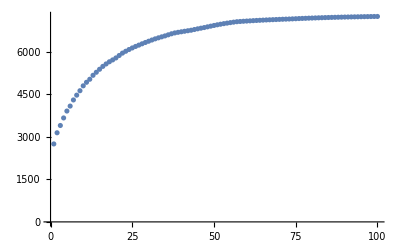

```mathematica
Table[IntegerPart[ifunc[curve⟦i⟧]],{i,1,Length@curve}]
```

```mathematica
d2fit=Transpose[{{0.0,8550.0,8650.0,8750.0,8850.0},
{0.0,270010.29942222434,277622.8485505647,283714.32931493793,289613.5229057922}}];
```

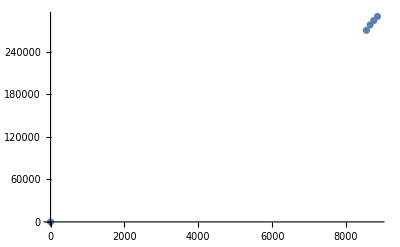

```mathematica
ListPlot[d2fit]
```

```mathematica
Fit[d2fit,{1,x,x^2},x]
```

-0.24624-0.445974 x+0.00375312 x^2

```mathematica
FullSimplify[c-b x+a x^2==y]
```

c+a x^2==b x+y

```mathematica
Factor[b x+a x^2]
```

x (b+a x)

```mathematica
Solve[c-b x+a x^2==y,x]
Solve[c+b x+a x^2==y,x]
```

{{x→(b-√(b^2-4 a c+4 a y))/(2 a)},{x→(b+√(b^2-4 a c+4 a y))/(2 a)}}

{{x→(-b-√(b^2-4 a c+4 a y))/(2 a)},{x→(-b+√(b^2-4 a c+4 a y))/(2 a)}}

```mathematica
(b-√(b^2-4 a c+4 a y))/(2 a)]
```

(b-√(b^2-4 a c+4 a y))/(2 a)

```mathematica
a=0.0037531194886177063;
b=-0.44597359070178305;
c=-0.24623967711853378;
(-b+√(b^2-4 a c+4 a 300000))/(2 a)
(-b-√(b^2-4 a c+4 a 300000))/(2 a)
```

9000.17

-8881.34

```mathematica
a=0.00293777026621
b=9.05840283365
c=-18770.2049156
√(b^2-4 a c+4 a 311986)
-b-√(b^2-4 a c+4 a 311986)
-b+√(b^2-4 a c+4 a 311986)
```

0.00293777

9.0584

-18770.2

62.9984

-72.0568

53.94

```mathematica
99554414790940424414351515490472769096534141749790794321708050837 104593961812606247801193807142122161186583731774511103180935025763
```

10412790658919985359827898739594318956404425106955675643739226952372682423852959081739834390370374475764863415203423499357108713631

```mathematica
Eigenvalues[{{0,0,0,0},{1,-1,1,1},{0,0,0,0},{0,0,0,0}}]
Eigenvectors[{{0,0,0,0},{1,-1,1,1},{0,0,0,0},{0,0,0,0}}]
```

{-1,0,0,0}

{{0,1,0,0},{-1,0,0,1},{-1,0,1,0},{1,1,0,0}}